# Vessel Segmentation

## Wenzhen Zhu WUSTL

## Notation

### Color Coding

RGBColor[0.98, 0.97, 0.5] | Equation
RGBColor[0.88, 1, 0.88] | My thoughts and explanations
RGBColor[1, 0.85, 0.85] | book segment 
RGBColor[1, 0.9, 0.8] | answer for the problem
RGBColor[1, 0.9, 1] | question
RGBColor[0.94, 0.88, 0.94] | assumption
RGBColor[0.87, 0.94, 1] | intermediate answer

## Intro

ArchHacks 2016  ‘s theme is HealthTech. 
I participate this hackathons and after building an app and talking to several medical students, I realized that I can actually apply what I learned from computer vision class and make some really world application to help patients who are suffering and to help doctors to be more efficient. That’s why I choose to do this project. 

Edge detection is an essential task in computer vision, and vessel segmentation is also an important task in clinical care and medical research. 

First, doctor can diagnose many disease from small change of vessels, like diabetes.  Second, some disease needs to remove vessels first in order to make further diagnosis.

## Style and Interface Code

```mathematica
pages676 = Import[NotebookDirectory[]<>"/1.svg.pdf"];
pages677 = Import[NotebookDirectory[]<>"/2.svg.pdf"];
```

## Related Work

### Morphology Operators

We define a 2D image whose range is [N_min, N_max] as a functional S:ℝ^2→[N_min,N_max]  and a 2-D structuring element as a functional B: ℝ^2→ B where B is the set of neighborhood of origin. 

We define basic operators, with respect to the structuring element B with scaling factor e, image S and point M_0∈ℝ^2

Because Mathematica Built-in function are optimized and calls C++, therefore, the built-in Erosion, Dilation, Opening, Closing, etc are extremely fast and reliable. I always compare the built-in function result with my own implementation result. My approach to prototyping the paper is to adapt Mathematica built-in functions, which takes kernel instead our habit - “offset structure element”, so I have a function that convert the offset structure element into kernel matrix. 

When I implement these functions in C++, I just copy the computed offset in the form of list of lists into “Morphology.h” and defined them as 2D array.

Erosion	(My C++ implementation has same result as Mathematica built-in Erosion)

ϵ_B^e(S)(M_0)= Min_(M∈M_0+ϵ B(M_0))(S(M))

Dilation	(My C++ implementation has same result as Mathematica built-in Dilation)

δ_B^e(S)(M_0)= Max_(M∈M_0+ϵ B(M_0))(S(M))

Opening	(My C++ implementation has same result as Mathematica built-in Opening)

γ_B^e(S)(M_0)= δ_B^e(ϵ_B^e(S))

Closing	(My C++ implementation has same result as Mathematica built-in Closing)

ϕ_B^e(S)(M_0)= ϵ_B^e(δ_B^e(S))

Top-hat	(My C++ implementation has same result as Mathematica built-in Top-hat)

TH_B^e(S)(M_0)= S - γ_B^e(S)

Geodesic dilation	(My C++ implementation has same result as Mathematica built-in GeodesicDilation)

S^1=inf({Max_(M∈M_0+c)(S_m(M))}, S(M_0))
S^(d+1)=Δ_S_m^(d+1)(S)(M_0)=Δ_S_m^1(S^d)(M_0)

Geodesic opening	(not sure, because Mathematica built-in GeodesicOpening doesn’t have maskImage argument)

γ_S_m^rec(S) = sup_(d∈ℕ) (Δ_S_m^d(S))

Geodesic closing	(not sure, because Mathematica built-in GeodesicClosing doesn’t have maskImage argument)

ϕ_S_m^rec(S) = N_max-γ_(N_max-S_m)^rec(N_max-S)

It’s quite hard for me (and TA) to understand several definitions as Geodesic Opening and Geodesic Closing. Here is page 676 - 677, Chapter 9: Morphological Image Processing

Compared to the paper, S^1=inf({Max_(M∈M_0+c)(S_m(M))}, S(M_0))
f = S_m = marker image, 
g = mask image, 
in the textbook, b means structure element. 
So for the geodesic dilation of size 1, I am confident with the operation, which is first, do dilation on marker image with a neighborhood C of unit radius, then selecting the minimum between dilation result and mask image.

I am not sure about the geodesic dilation of size n, the book defined as D_g^(n)(f)=D_g^(1)[D_g^(n-1)(f)]

so when I implement this method in C++, I used the book’s definition because I don’t quite understand the paper’s notation.
I compared the result of this implementation on some random pixel, which gives me same result as Mathematica built-in GeodesicDilation.

CFloatImage GeodesicDilation(CFloatImage marker, CFloatImage mask, int size) {
	int marker_w = marker.Shape().width;
	int marker_h = marker.Shape().height;
	CFloatImage resultImage(marker.Shape());
	
	// base case
	if (size == 0) {
		return marker;
	}
	if (size == 1) {
		CFloatImage DilationImage = DilationStructSquare(marker);
		for (int x = 0; x < marker_w; x++) {
			for (int y = 0; y < marker_h; y++) {
				//In the paper, geodesic dilation used normal dilation in the base case;
				// S1(M0) = inf({Dilation, S(M0)})
				resultImage.Pixel(x, y, 0) = min(DilationImage.Pixel(x, y, 0), mask.Pixel(x, y, 0));
			}
		} 
		return resultImage;
	}
	return GeodesicDilation(GeodesicDilation(marker, mask, size - 1), mask, 1);
}

## Algorithms

```mathematica
dir=NotebookDirectory[];
img=ColorConvert[Import[dir<>"DRIVE/training/images/21_training.tif"],"Grayscale"];
imgData=ImageData[img,"Byte"];
```

### Step 0: Construct L_i

This paper is interesting because it used a linear structure element L_i which is 15-pixels long 1-pixel wide.

```mathematica
angles=Table[{Cos[t],Sin[t]},{t,0,11π/12,π/12}]
```

{{1,0},{(1+√3)/(2 √2),(-1+√3)/(2 √2)},{(√3)/2,1/2},{1/(√2),1/(√2)},{1/2,(√3)/2},{(-1+√3)/(2 √2),(1+√3)/(2 √2)},{0,1},{-(-1+√3)/(2 √2),(1+√3)/(2 √2)},{-1/2,(√3)/2},{-1/(√2),1/(√2)},{-(√3)/2,1/2},{-(1+√3)/(2 √2),(-1+√3)/(2 √2)}}

For every π/12, there is an linear structure element.

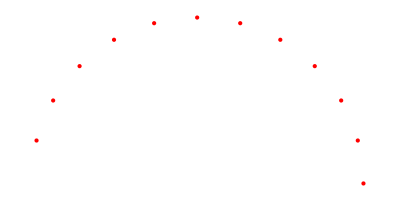

```mathematica
Graphics[{Red,PointSize->Large,Point[angles]}]
```

```mathematica
linearStrut=Table[Round[{Cos[t],Sin[t]}* #] &/@(Range[15]-8),{t,0,11π/12,π/12}];
```

Here is a visualization of the structure element.

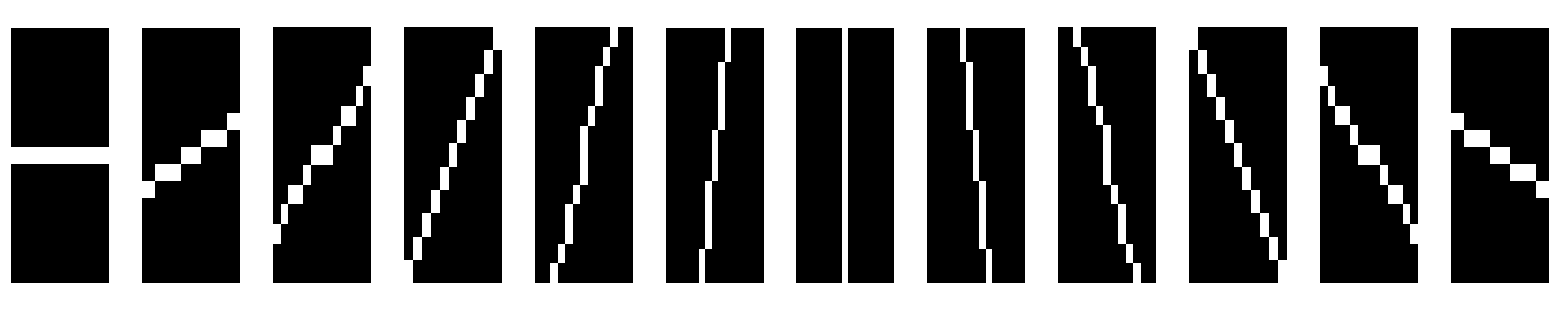

```mathematica
GraphicsRow[showBinaryImage[kernelFromStructure[#]]&/@linearStrut]
```

```mathematica
kernels=kernelFromStructure[#]&/@linearStrut
```

{{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0}},{{1,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,1}},{{0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0}},{{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0}},{{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,1,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,1,1,1,1,0,0},{0,0,0,0,0,0,1,1,1,0,0,0,0,0,0},{0,0,1,1,1,1,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}

### Step 1

#### Calculating S_op

The first step is calculating S_op, which can be summarized in the followings:
1. Opening with 12 structure element on S_0(original images)
2. Pick the maximum from these 12 images pixel-wise and form a maximum image
3. Do geodesic opening on the maximum image, the result will be our S_op

S_op=γ_S_0^rec(Max_(i = 1, .., 12){γ_L_i(S_0)})

```mathematica
openingImageList=Opening[img,#]&/@kernels
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AbsoluteTiming[openingDataList=ImageData[#]&/@openingImageList]
```

{0.0313,{{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}}
 |  |  |  |

```mathematica
maxOpeningData=MapThread[Max,openingDataList,2]
```

{1}
 |  |  |  |

```mathematica
maxOpeningImage=Image[maxOpeningData]
```

-Graphics-

```mathematica
markerImage=img;
mask=maxOpeningImage;
```

```mathematica
SopData=geodesicOpening[markerImage,mask]
```

{1}
 |  |  |  |

Here is a visualized result S_opimage.

```mathematica
SopImage=Image[SopData]
```

-Graphics-

### Step 2

#### Calculating S_sum

This transformation (a sum of top hats) reduces small bright noise and improves the contrast of all linear parts. Vessels could be manually segmented with a simple threshold on S_sum

S_sum:=∑_(i=1)^12 (S_op-γ_L_i(S_0))

The second step is calculating S_sum, which can be summarized in the followings:
1. Opening with 12 structure element on S_0(original images).
2. Use S_op  to minus the opening images pixel-wise.
3. Sum the 12 difference image up to get S_sumimage

```mathematica
AbsoluteTiming[topHatData=(SopData-#)&/@openingDataList]
```

{0.170847,{{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}}
 |  |  |  |

```mathematica
AbsoluteTiming[SsumData=Total[topHatData]]
```

{0.013569,{1}}
 |  |  |  |

```mathematica
SsumImage=Image[SsumData]
```

-Graphics-

### Step 3

This step is very straight forward:
1. Apply Gaussian filter with r = 7 and σ = 7/4
2. Apply Laplacian filter with r = 1.

S_lap=Laplacian(Gaussian_(σ = 7/4)^(width = 7px)(S_sum))

#### Applying Gaussian filter

```mathematica
gaussianImage=GaussianFilter[SsumImage,{7,7/4}]
```

-Graphics-

#### Applying Laplacian filter

```mathematica
SlapImage=LaplacianFilter[gaussianImage,1]
```

-Graphics-

### Step 4

#### Calculating S_1

This step can be summarized in the followings:
1. Opening with 12 structure element on S_lap(Laplacian applied image).
2. Pick the maximum from these 12 images pixel-wise and form a maximum image
3. Do geodesic opening on the maximum image, the result will be our S_1

S_1=γ_S_lap^rec(Max_(i=1,...12){γ_L_i(S_lap)})

```mathematica
AbsoluteTiming[openingOnSlapData=ImageData/@(Opening[SlapImage,#]&/@kernels)]
```

{0.213361,{{1},10,{{0.000290349,0.000318456,0.000355327,0.000355327,0.000355327,0.000267228,0.00015834,552,0.0000839143,0.0000715021,0.0000585977,0.0000535731,0.0000487266,0.0000456603},582,{1}}}}
 |  |  |  |

Pick the maximum

```mathematica
maxOpeningOnSlapData=MapThread[Max,openingOnSlapData,2];
```

```mathematica
maxOpeningOnSlapImage=Image[maxOpeningOnSlapData]
```

-Graphics-

Apply Geodesic opening on the maximum

```mathematica
S1Data=geodesicOpening[SlapImage,maxOpeningOnSlapImage]
```

{{0.000290349,0.000318456,0.000358895,0.000383397,0.000355327,0.000267228,0.00015834,0.0000754616,550,0.000158945,0.0000839143,0.0000715021,0.0000585977,0.0000535731,0.0000487266,0.0000456603},582,{1}}
 |  |  |  |

```mathematica
S1=Image[S1Data]
```

-Graphics-

#### Calculating S_2

This step can be summarized in the followings:
1. Closing with 12 structure element on S_1.
2. Pick the minimum from these 12 images pixel-wise and form an image.
3. Do geodesic closing with marker being S_1, mask being the minimum image.

S_2=ϕ_S_1^rec(Min_(i=1,...,12){ϕ_L_i(S_1)})

```mathematica
AbsoluteTiming[closingImageList=Closing[S1,#]&/@kernels]
```

{0.240477,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
AbsoluteTiming[closingDataList=ImageData/@closingImageList]
```

{0.000021,{{1},{{0.000703308,0.000703308,0.000550335,0.000383397,0.000355327,0.000355327,553,0.000189741,0.000189741,0.000189741,0.0000535731,0.0000487266,0.0000487266},582,{1}},9,{1}}}
 |  |  |  |

```mathematica
minClosingData=MapThread[Min,closingDataList,2];
```

```mathematica
minClosingImage=Image[minClosingData]
```

-Graphics-

```mathematica
S2Data=geodesicClosing[S1Data,minClosingData]
```

{{0.000290349,0.000318456,0.000358895,0.000383397,0.000355327,0.000267228,0.00015834,0.0000754616,550,0.000158945,0.0000839143,0.0000715021,0.0000585977,0.0000535731,0.0000487266,0.0000456603},582,{1}}
 |  |  |  |

```mathematica
S2=Image[S2Data]
```

-Graphics-

#### Calculating S_res

This step can be summarized in the followings:
1. Opening with 12 structure, r = 2 indicates the structure element 29 pixels long, 1 pixel wide on S_1.
2. Pick the maximum from these 12 images pixel-wise and form an image.
3. If the pixel value ≥ 1, assign 1 on that pixel, otherwise assign 0.

S_res=(Max_(i = 1..12){γ_L_i^2(S_2)}≥1)

#### scaling e = 2

```mathematica
linearStruct2=Table[Round[{Cos[t],Sin[t]}* #] &/@(Range[29]-15),{t,0,11π/12,π/12}]
```

{{{-14,0},{-13,0},{-12,0},{-11,0},{-10,0},{-9,0},{-8,0},{-7,0},{-6,0},{-5,0},{-4,0},{-3,0},{-2,0},{-1,0},{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0}},{{-14,-4},{-13,-3},{-12,-3},{-11,-3},{-10,-3},{-9,-2},{-8,-2},{-7,-2},{-6,-2},{-5,-1},{-4,-1},{-3,-1},{-2,-1},{-1,0},{0,0},{1,0},{2,1},{3,1},{4,1},{5,1},{6,2},{7,2},{8,2},{9,2},{10,3},{11,3},{12,3},{13,3},{14,4}},{{-12,-7},{-11,-6},{-10,-6},{-10,-6},{-9,-5},{-8,-4},{-7,-4},{-6,-4},{-5,-3},{-4,-2},{-3,-2},{-3,-2},{-2,-1},{-1,0},{0,0},{1,0},{2,1},{3,2},{3,2},{4,2},{5,3},{6,4},{7,4},{8,4},{9,5},{10,6},{10,6},{11,6},{12,7}},{{-10,-10},{-9,-9},{-8,-8},{-8,-8},{-7,-7},{-6,-6},{-6,-6},{-5,-5},{-4,-4},{-4,-4},{-3,-3},{-2,-2},{-1,-1},{-1,-1},{0,0},{1,1},{1,1},{2,2},{3,3},{4,4},{4,4},{5,5},{6,6},{6,6},{7,7},{8,8},{8,8},{9,9},{10,10}},{{-7,-12},{-6,-11},{-6,-10},{-6,-10},{-5,-9},{-4,-8},{-4,-7},{-4,-6},{-3,-5},{-2,-4},{-2,-3},{-2,-3},{-1,-2},{0,-1},{0,0},{0,1},{1,2},{2,3},{2,3},{2,4},{3,5},{4,6},{4,7},{4,8},{5,9},{6,10},{6,10},{6,11},{7,12}},{{-4,-14},{-3,-13},{-3,-12},{-3,-11},{-3,-10},{-2,-9},{-2,-8},{-2,-7},{-2,-6},{-1,-5},{-1,-4},{-1,-3},{-1,-2},{0,-1},{0,0},{0,1},{1,2},{1,3},{1,4},{1,5},{2,6},{2,7},{2,8},{2,9},{3,10},{3,11},{3,12},{3,13},{4,14}},{{0,-14},{0,-13},{0,-12},{0,-11},{0,-10},{0,-9},{0,-8},{0,-7},{0,-6},{0,-5},{0,-4},{0,-3},{0,-2},{0,-1},{0,0},{0,1},{0,2},{0,3},{0,4},{0,5},{0,6},{0,7},{0,8},{0,9},{0,10},{0,11},{0,12},{0,13},{0,14}},{{4,-14},{3,-13},{3,-12},{3,-11},{3,-10},{2,-9},{2,-8},{2,-7},{2,-6},{1,-5},{1,-4},{1,-3},{1,-2},{0,-1},{0,0},{0,1},{-1,2},{-1,3},{-1,4},{-1,5},{-2,6},{-2,7},{-2,8},{-2,9},{-3,10},{-3,11},{-3,12},{-3,13},{-4,14}},{{7,-12},{6,-11},{6,-10},{6,-10},{5,-9},{4,-8},{4,-7},{4,-6},{3,-5},{2,-4},{2,-3},{2,-3},{1,-2},{0,-1},{0,0},{0,1},{-1,2},{-2,3},{-2,3},{-2,4},{-3,5},{-4,6},{-4,7},{-4,8},{-5,9},{-6,10},{-6,10},{-6,11},{-7,12}},{{10,-10},{9,-9},{8,-8},{8,-8},{7,-7},{6,-6},{6,-6},{5,-5},{4,-4},{4,-4},{3,-3},{2,-2},{1,-1},{1,-1},{0,0},{-1,1},{-1,1},{-2,2},{-3,3},{-4,4},{-4,4},{-5,5},{-6,6},{-6,6},{-7,7},{-8,8},{-8,8},{-9,9},{-10,10}},{{12,-7},{11,-6},{10,-6},{10,-6},{9,-5},{8,-4},{7,-4},{6,-4},{5,-3},{4,-2},{3,-2},{3,-2},{2,-1},{1,0},{0,0},{-1,0},{-2,1},{-3,2},{-3,2},{-4,2},{-5,3},{-6,4},{-7,4},{-8,4},{-9,5},{-10,6},{-10,6},{-11,6},{-12,7}},{{14,-4},{13,-3},{12,-3},{11,-3},{10,-3},{9,-2},{8,-2},{7,-2},{6,-2},{5,-1},{4,-1},{3,-1},{2,-1},{1,0},{0,0},{-1,0},{-2,1},{-3,1},{-4,1},{-5,1},{-6,2},{-7,2},{-8,2},{-9,2},{-10,3},{-11,3},{-12,3},{-13,3},{-14,4}}}

```mathematica
GraphicsRow[showBinaryImage[kernelFromStructure[#]]&/@linearStruct2]
```

-Graphics-

```mathematica
kernels2=kernelFromStructure[#]&/@linearStruct2;
```

```mathematica
openingOnS2=Opening[S2,#]&/@kernels2
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
openingOnS2Data=ImageData/@openingOnS2
```

{{{0.0000166485,0.0000166485,0.0000166485,0.0000166485,0.0000166485,0.0000166485,0.0000166485,0.0000166485,0.0000166485,0.0000166485,0.0000166485,0.0000252046,541,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},583},11}
 |  |  |  |

```mathematica
SresData=MapThread[Max,openingOnS2Data,2];
```

```mathematica
sres=Image[SresData]
```

-Graphics-

```mathematica
sresByte=ImageData[sres,"Byte"]
```

{1}
 |  |  |  |

```mathematica
convertToBinary[x_]:=If[x≥1,1,0]
```

```mathematica
result=(convertToBinary/@sresByte[[#]])&/@Range[Length[sresByte]]
```

{1}
 |  |  |  |

```mathematica
Image[result]
```

-Graphics-

## Summary

This paper is supposed to be very basic morphology’s application. But I am very sorry that I didn’t get the expected result. 

I checked both my Mathematica prototyping and C++ implementation over and over again. 
The possible mistakes could happen are as followings, I still need more time to check them or talk to people who are more experienced in this field.

1. From GeodesicOpening/Closing, I cannot check my implementation with Mathematica built-in functions anymore because Mathematica built-in function has different arguments. (It doesn’t take mask image, only marker image)
2. Therefore, to follow the paper, I need to implement geodesicOpening/closing in Mathematica myself. 
	From my understanding, geodesic opening is by applying geodesic dilations on original image (gray) with a marker image (doesn’t change) again and again until it gets “stable” (all pixels don’t change anymore). 
	Then from a list of geodesic dilated images, we can pick the maximum point-wise, which will give us the geodesic opening result. 
	Geodesic closing is very straightforward hence easy to implement if Geodesic opening is correct.
	I used FixedPointList function in Mathematica, which should work exactly as the theory described.
	I used a threshold = 10^-3 in C++, since I cannot compare two floating number are equal directly. 
	
3. GaussianFilter
	Mathematica’s kernel for GaussianFilter is probably normalized. But the ratio between GaussianFilter’s result and GaussianKernel’s result is the same. 
	My question is, is that really so easy? The paper didn’t include a parameter in the kernel. And I don’t quite understand section III. C. Evaluation of the Curvature using the Laplacian.

## Future Direction

For glaucoma detection, there is one approach from a paper which extract the optic disk first, then replace vessels, because vessels are regarded as noises. I already implement the first step that extract the optic disk automatically. I will implement this paper as well.

Google Brain is working on similar things

I think the most important thing is what theory I learned from this paper. I built an App this semester doing segmentation on Corneal Ulcer eyes. But the algorithm I developed is to the binarize on a threshold first and do morphology operations on binary images. Which works well for the fluorescent images but not working well on images under natural lights. I want to try using the morphology I learned from this paper to solve the natural light problem. There are three medical school students promised me to give me images for testing.